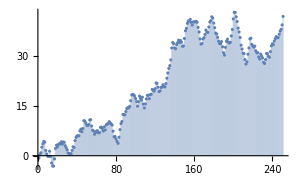

| Statistic | P-Value
Dickey-Fuller F | 1.0837 | 0.924905

| Statistic | P-Value
Dickey-Fuller F | -126.572 | 4.06991×10^-10

```mathematica
SeedRandom[456346435];
data=RandomFunction[ARIMAProcess[{.3},1,{.2},1],{0,250}]["PathStates"];
ListPlot[data,Filling->Axis,ImageSize->300]
UnitRootTest[data,Automatic,"TestDataTable"]
UnitRootTest[Differences[data],Automatic,"TestDataTable"]
```